Piecewise[{{1, t<0}, {ⅇ^(-2587 t/500000000) (1-(1-ⅇ^(-137 t/40000000))^2) (1-(1-ⅇ^(-t/500000))^2) (1-(1-ⅇ^(-181 t/500000000))^2)^2 (ⅇ^(-873 t/500000000)+ⅇ^(-291 t/500000000) (-ⅇ^(-873 t/500000000)+ⅇ^(-291 t/250000000)+ⅇ^(-291 t/500000000) (-ⅇ^(-291 t/250000000)+ⅇ^(-291 t/500000000)+ⅇ^(-291 t/500000000) (1-ⅇ^(-291 t/500000000))))), True}}]

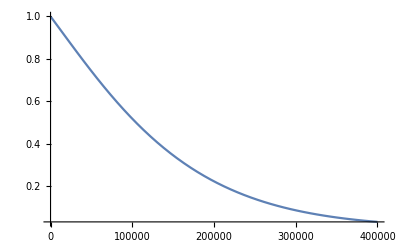

132564.

{0.99997,0.999819,0.999457}

15.1329

```mathematica
removeAll:=Remove[Evaluate[$Context<>"*"]];

removeAll

(* Считаем для сервера RH1288 *)
Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"HDD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[3425×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1];
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (*CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (*RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh1288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh1288,t]
Plot[SurvivalFunction[ℛrh1288,t]//Evaluate,{t,0,400000},PlotRange->All]
mttf=NExpectation[t,t\[Distributed]ℛrh1288]
avail = mttf/(mttf+{4,24,72})
Mean[ℛrh1288]/(24*365)//N
```